Runge - Kutta (Explicitní)

```mathematica
g:=9.81
l:=1
```

Perioda v závisloti na počáteční podmínce:

```mathematica
Period[θinit_]:=(time:=0;
NDSolve[{θ''[t]+g/l Sin[θ[t]] ==0,θ[0]== θinit,θ'[0]==0,WhenEvent[θ[t]==0,{time = t, "StopIntegration"}]},θ,{t,0,3 },Method->"ExplicitRungeKutta"];
4*time)
```

```mathematica
Tabulka = Table[{θinit, Period[θinit]}, {θinit,1/1000, Pi/2, 0.1 }]
body:=ListPlot[Tabulka,PlotTheme->"NeonColor"]
```

{{0.001,2.00607},{0.101,2.00735},{0.201,2.01114},{0.301,2.01749},{0.401,2.02642},{0.501,2.038},{0.601,2.05231},{0.701,2.06947},{0.801,2.0896},{0.901,2.11285},{1.001,2.13942},{1.101,2.16953},{1.201,2.20344},{1.301,2.24148},{1.401,2.28401},{1.501,2.33149}}

```mathematica
fit1 =Fit[ Tabulka, {1, x^2,  x^4, x^6}, x]
polynom := Plot[fit1,{x,0, Pi/2}, PlotTheme->"PastelColor", PlotLegends->{"proložení dat"}]
```

2.00606+0.125509 x^2+0.00688717 x^4+0.000672197 x^6

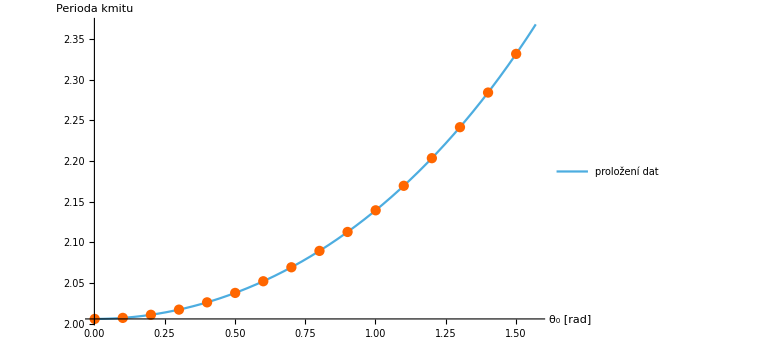

```mathematica
Show[polynom, body,AxesLabel->{"θ_0 [rad]", "Perioda kmitu"},ImageSize->Large]
```

Fázový diagram:

```mathematica
system :=NDSolve[{x'[t]==y[t],y'[t]==-g/l Sin[x[t]],x[0]== Pi/2,y[0]==0},{x[t],y[t]},{t,0,10000},Method->"ExplicitRungeKutta"]
```

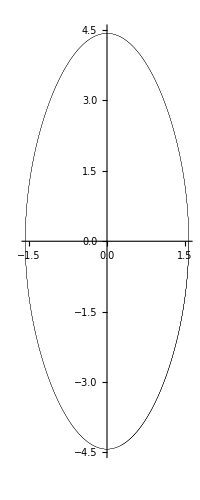

```mathematica
ParametricPlot[Evaluate[{x[t], y[t]} /. system], {t, 0, 10}, PlotTheme->"Monochrome", PlotStyle->Thickness[0.000001]]
```

Energie systému:

```mathematica
sol:=NDSolve[{θ''[t]+g/l Sin[θ[t]] ==0,θ[0]== Pi/2,θ'[0]==0},θ,{t,0,10000 },Method->"ExplicitRungeKutta"]
```

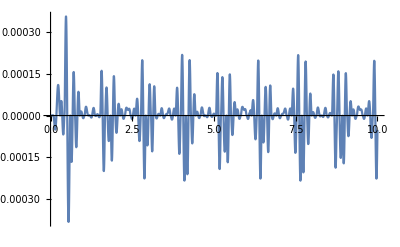

```mathematica
Plot[Evaluate[((θ'[t])^2 /2 -g/l * Cos[θ[t]])/. sol],{t,0,10},PlotRange->All,PlotLegends->"Energie"]
```